## Input

### Derivatives of Shape Function

```mathematica
hhp=({{-1.5, -0.5, 0.5}, {2, 0, -2}, {-0.5, 0.5, 1.5}});
(*hhp=Transpose[hhp];*)
```

### Weight Function

```mathematica
wj=({{1.0/3}, {4.0/3}, {1.0/3}});
```

### Beam Length and Cross-Section Constants

```mathematica
L=1;
EA=10^4;
GA=10^4;
EI=10^2;
(*EA=70*10^9;
GA=5.*27*10^9/6.;
EI=70*10^9/12.;*)
Stif0=Table[0,{i,6},{j,6}];
Stif0[[1,1]]=3.50000*10^8;
Stif0[[2,2]]=1.09162*10^8;
Stif0[[3,3]]=1.09162*10^8;
Stif0[[4,4]]=7.57037*10^4;
Stif0[[5,5]]=7.28000*10^4;
Stif0[[6,6]]=2.91900*10^5;
m00=1.35*10^1;
mEta0=({{0}, {0}, {0}});
rho0=({{1.40625*10^-2, 0, 0}, {0, 2.81250*10^-3, 0}, {0, 0, 1.12500*10^-2}});
```

### Jacobian and Initial Value

```mathematica
Jaco=L/2;
uuNf={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
uuN0={{0.},{0},{0},{0},{0},{0},{0.5},{0},{0},{0},{0},{0},{1.0},{0},{0},{0},{0},{0}};
uuNi={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
vvNi={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
aaNi={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
xxNi={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
vvNf={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
aaNf={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
xxNf={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
tolx=1.0*10^-6;
```

### Sin Force Function

```mathematica
Af=1.0*10^5;
ωf=20;
Fext[t_]:=Af*Sin[ωf*t];
```

## Utilities

```mathematica
Tilde[v1_,v2_,v3_]:=Module[{m12,m13,m21,m23,m31,m32},
m12=-v3;m13=v2;
m21=v3;m23=-v1;
m31=-v2;m32=v1;
{{0,m12,m13},{m21,0,m23},{m31,m32,0}}]
```

## CRV Functions

### CRV Compose 0

```mathematica
CrvCompose0[cc1_,cc2_,cc3_,c01_,c02_,c03_]:=Module[{pp0,pp1=cc1,pp2=cc2,pp3=cc3,qq0,qq1=c01,qq2=c02,qq3=c03,tr1,tr2,dd1,dd2,c1,c2,c3},
pp0=2.0-(pp1*pp1+pp2*pp2+pp3*pp3)/8;
qq0=2.0-(qq1*qq1+qq2*qq2+qq3*qq3)/8;
tr1=(4-pp0)*(4-qq0);
tr2=pp0*qq0-pp1*qq1-pp2*qq2-pp3*qq3;
dd1=tr1+tr2;
dd2=tr1-tr2;
If[dd1>dd2,tr1=4/dd1,tr1=-4/dd2];
c1=tr1*(pp1*qq0+pp0*qq1-pp3*qq2+pp2*qq3);
c2=tr1*(pp2*qq0+pp3*qq1+pp0*qq2-pp1*qq3);
c3=tr1*(pp3*qq0-pp2*qq1+pp1*qq2+pp0*qq3);
{{c1},{c2},{c3}}];
```

### CRV Compose 1

```mathematica
CrvCompose1[cc1_,cc2_,cc3_,c01_,c02_,c03_]:=Module[{pp0,pp1=-cc1,pp2=-cc2,pp3=-cc3,qq0,qq1=c01,qq2=c02,qq3=c03,tr1,tr2,dd1,dd2,c1,c2,c3},
pp0=2.0-(pp1*pp1+pp2*pp2+pp3*pp3)/8;
qq0=2.0-(qq1*qq1+qq2*qq2+qq3*qq3)/8;
tr1=(4-pp0)*(4-qq0);
tr2=pp0*qq0-pp1*qq1-pp2*qq2-pp3*qq3;
dd1=tr1+tr2;
dd2=tr1-tr2;
If[dd1>dd2,tr1=4/dd1,tr1=-4/dd2];
c1=tr1*(pp1*qq0+pp0*qq1-pp3*qq2+pp2*qq3);
c2=tr1*(pp2*qq0+pp3*qq1+pp0*qq2-pp1*qq3);
c3=tr1*(pp3*qq0-pp2*qq1+pp1*qq2+pp0*qq3);
{{c1},{c2},{c3}}];
```

### CRV Matrix R

```mathematica
CrvMatrixR[cc1_,cc2_,cc3_]:=Module[{c0,c1=cc1/4,c2=cc2/4,c3=cc3/4,tr0,R0,R1,R2,R3,R4,R5,R6,R7,R8},
c0=0.5*(1-c1*c1-c2*c2-c3*c3);
tr0=1-c0;
tr0=2/(tr0*tr0);
R0=tr0*(c1*c1+c0*c0)-1;
R1=tr0*(c1*c2+c0*c3);
R2=tr0*(c1*c3-c0*c2);
R3=tr0*(c1*c2-c0*c3);
R4=tr0*(c2*c2+c0*c0)-1;
R5=tr0*(c2*c3+c0*c1);
R6=tr0*(c1*c3+c0*c2);
R7=tr0*(c2*c3-c0*c1);
R8=tr0*(c3*c3+c0*c0)-1;
{{R0,R3,R6},{R1,R4,R7},{R2,R5,R8}}];
```

### CRV Matrix H

```mathematica
CrvMatrixH[cc1_,cc2_,cc3_]:=Module[{cf1=cc1/4,cf2=cc2/4,cf3=cc3/4,cq,ocq,aa,cb0,cb1,cb2,cb3,H0,H1,H2,H3,H4,H5,H6,H7,H8},
cq=cf1*cf1+cf2*cf2+cf3*cf3;
ocq=1+cq;
aa=2*ocq*ocq;
cb0=2*(1-cq)/aa;
cb1=cc1/aa;
cb2=cc2/aa;
cb3=cc3/aa;
H0=cb1*cf1+cb0;
H1=cb2*cf1+cb3;
H2=cb3*cf1-cb2;
H3=cb1*cf2-cb3;
H4=cb2*cf2+cb0;
H5=cb3*cf2+cb1;
H6=cb1*cf3+cb2;
H7=cb2*cf3-cb1;
H8=cb3*cf3+cb0;
{{H0,H3,H6},{H1,H4,H7},{H2,H5,H8}}];
```

## GLL Shape Function

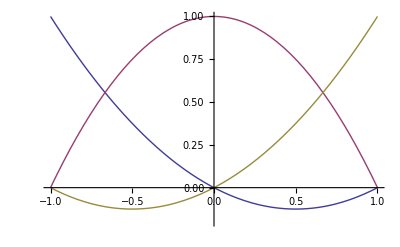

```mathematica
norder=2;
GLL1=-1.0;
GLL2=0.0;
GLL3=1.0;
GL1=-Sqrt[3]/3.0;
GL2=Sqrt[3]/3.0;
hh1[s_]:=Piecewise[{{1,s==GLL1},{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL1]*(s-GLL1)),GLL1<s≤1}}];
hh2[s_]:=Piecewise[{{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL2]*(s-GLL2)),-1≤s<GLL2},{1,s==GLL2},{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL2]*(s-GLL2)),GLL2<s≤1}}];
hh3[s_]:=Piecewise[{{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL3]*(s-GLL3)),-1≤s<GLL3},{1,s==GLL3}}];
Plot[{hh1[s],hh2[s],hh3[s]},{s,-1,1},PlotRange->{{-1,1},{-0.2,1}}]
```

## Time Scheme Parameters and Coefficients

```mathematica
rhoinf=0.0;
```

```mathematica
tr0=rhoinf+1.0;
alfam=(2.0*rhoinf-1.0)/tr0;
alfaf=rhoinf/tr0;
gama=0.5-alfam+alfaf;
beta=0.25*(1.0-alfam+alfaf)^2;
```

```mathematica
deltat=0.001;
deltat2=deltat^2;
```

```mathematica
oalfaM=1.0-alfam;
tr0=alfaf/oalfaM;
tr1=alfam/oalfaM;
tr2=(1.0-alfaf)/oalfaM;
coef={{0},{0},{0},{0},{0},{0},{0},{0},{0}};
coef[[1,1]]=beta*tr0*deltat2;
coef[[2,1]]=(0.5-beta/oalfaM)*deltat2;
coef[[3,1]]=gama*tr0*deltat;
coef[[4,1]]=(1.0-gama/oalfaM)*deltat;
coef[[5,1]]=tr0;
coef[[6,1]]=-tr1;
coef[[7,1]]=gama*tr2*deltat;
coef[[8,1]]=beta*tr2*deltat2;
coef[[9,1]]=tr2;
coef
```

{{0.},{0.},{0.},{0.00025},{0.},{0.5},{0.00075},{5.×10^-7},{0.5}}

## First Iteration

### (*Predictor Step*)

```mathematica
vvNf=vvNi+coef[[3,1]]*aaNi+coef[[4,1]]*xxNi;
aaNf=Table[0,{i,18},{j,1}];
xxNf=coef[[5,1]]*aaNi+coef[[6,1]]*xxNi;
tr=Table[0,{i,1,18},{j,1}];
tr=deltat*vvNi+coef[[1,1]]*aaNi+coef[[2,1]]*xxNi;
tempN1=CrvCompose0[tr[[4,1]],tr[[5,1]],tr[[6,1]],uuNi[[4,1]],uuNi[[5,1]],uuNi[[6,1]]];
tempN2=CrvCompose0[tr[[10,1]],tr[[11,1]],tr[[12,1]],uuNi[[10,1]],uuNi[[11,1]],uuNi[[12,1]]];
tempN3=CrvCompose0[tr[[16,1]],tr[[17,1]],tr[[18,1]],uuNi[[16,1]],uuNi[[17,1]],uuNi[[18,1]]];
Do[uuNf[[i,1]]=uuNi[[i,1]]+tr[[i,1]],{i,3}]
Do[uuNf[[i+3,1]]=tempN1[[i,1]],{i,3}];
Do[uuNf[[i+6,1]]=tr[[i+6,1]],{i,3}];
Do[uuNf[[i+3+6,1]]=tempN2[[i,1]],{i,3}];
Do[uuNf[[i+12,1]]=tr[[i+12,1]],{i,3}];
Do[uuNf[[i+3+12,1]]=tempN3[[i,1]],{i,3}];
```

### (*END Predictor Step*)

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm
E10N2//MatrixForm
E10N3//MatrixForm
```

(1.
0.
0.)

(1.
0.
0.)

(1.
0.
0.)

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm;
E1N2//MatrixForm;
E1N3//MatrixForm;
```

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]];
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]];
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]];
```

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm;
RR0N2//MatrixForm;
RR0N3//MatrixForm;
```

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
```

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm;
```

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]]; 
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]]; 
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]];
```

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm;
rrpN2 // MatrixForm;
rrpN3 // MatrixForm;
```

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN2.rrpN3;
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm;
```

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm;
kapaN2 // MatrixForm;
kapaN3 // MatrixForm;
```

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cet*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cet*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cet*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cet*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cet*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cet*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm;
FcN2//MatrixForm;
FcN3//MatrixForm;
FdN1//MatrixForm;
FdN2//MatrixForm;
FdN3//MatrixForm;
```

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
(*Check Output*)
QeN3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 1.09162×10^8 | 0.
0 | 0 | 0 | 0. | 0. | 1.09162×10^8)

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Rotate Mass Constants mEta0 and rho0*)

```mathematica
tempR3=Table[0,{i,3},{j,3}];
mEtaN1=Table[0,{i,3},{j,1}];
mEtaN2=Table[0,{i,3},{j,1}];
mEtaN3=Table[0,{i,3},{j,1}];
rhoN1=Table[0,{i,3},{j,3}];
rhoN2=Table[0,{i,3},{j,3}];
rhoN3=Table[0,{i,3},{j,3}];
Do[tempR3[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
mEtaN1=tempR3.mEta0;
rhoN1=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
mEtaN2=tempR3.mEta0;
rhoN2=tempR3.rho0.Transpose[tempR3];
Do[tempR3[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
mEtaN3=tempR3.mEta0;
rhoN3=tempR3.rho0.Transpose[tempR3];
```

### (*END Rotate Mass Constants mEta0 and rho0*)

### (*Compute Inertial Forces: Mi, Fi, Ki, Gi*)

```mathematica
omeN1=Table[0,{i,3},{j,1}];
omeN2=Table[0,{i,3},{j,1}];
omeN3=Table[0,{i,3},{j,1}];
omdN1=Table[0,{i,3},{j,1}];
omdN2=Table[0,{i,3},{j,1}];
omdN3=Table[0,{i,3},{j,1}];
tempVN1=Table[0,{i,3},{j,1}];
tempVN2=Table[0,{i,3},{j,1}];
tempVN3=Table[0,{i,3},{j,1}];
tempAN1=Table[0,{i,3},{j,1}];
tempAN2=Table[0,{i,3},{j,1}];
tempAN3=Table[0,{i,3},{j,1}];
Do[omeN1[[i,1]]=vvNf[[i+3,1]],{i,3}];
Do[omeN2[[i,1]]=vvNf[[i+3+6,1]],{i,3}];
Do[omeN3[[i,1]]=vvNf[[i+3+12,1]],{i,3}];
Do[omdN1[[i,1]]=aaNf[[i+3,1]],{i,3}];
Do[omdN2[[i,1]]=aaNf[[i+3+6,1]],{i,3}];
Do[omdN3[[i,1]]=aaNf[[i+3+12,1]],{i,3}];
Do[tempVN1[[i,1]]=vvNf[[i,1]],{i,3}];
Do[tempVN2[[i,1]]=vvNf[[i+6,1]],{i,3}];
Do[tempVN3[[i,1]]=vvNf[[i+12,1]],{i,3}];
Do[tempAN1[[i,1]]=aaNf[[i,1]],{i,3}];
Do[tempAN2[[i,1]]=aaNf[[i+6,1]],{i,3}];
Do[tempAN3[[i,1]]=aaNf[[i+12,1]],{i,3}];
```

```mathematica
FiN1=Table[0,{i,6},{j,1}];
betaN1=Table[0,{i,3},{j,1}];
betaN2=Table[0,{i,3},{j,1}];
betaN3=Table[0,{i,3},{j,1}];
gamaN1=Table[0,{i,3},{j,1}];
gamaN2=Table[0,{i,3},{j,1}];
gamaN3=Table[0,{i,3},{j,1}];
nuN1=Table[0,{i,3},{j,1}];
nuN2=Table[0,{i,3},{j,1}];
nuN3=Table[0,{i,3},{j,1}];
betaN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].mEtaN1;
gamaN1=rhoN1.omeN1;
nuN1=rhoN1.omdN1;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN1+Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].mEtaN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].betaN1;
Do[FiN1[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]].tempAN1+nuN1+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].gamaN1;
Do[FiN1[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN2=Table[0,{i,6},{j,1}];
betaN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].mEtaN2;
gamaN2=rhoN2.omeN2;
nuN2=rhoN2.omdN2;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN2+Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].mEtaN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].betaN2;
Do[FiN2[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]].tempAN2+nuN2+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].gamaN2;
Do[FiN2[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3=Table[0,{i,6},{j,1}];
betaN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].mEtaN3;
gamaN3=rhoN3.omeN3;
nuN3=rhoN3.omdN3;
temp3=Table[0,{i,3},{j,1}];
temp3=m00*tempAN3+Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].mEtaN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].betaN3;
Do[FiN3[[i,1]]=temp3[[i,1]],{i,3}];
temp3=Table[0,{i,3},{j,1}];
temp3=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]].tempAN3+nuN3+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].gamaN3;
Do[FiN3[[i+3,1]]=temp3[[i,1]],{i,3}];
FiN3//MatrixForm
```

(0.
0.
0.
0.
0.
0.)

```mathematica
MiN1=Table[0,{i,6},{j,6}];
MiN2=Table[0,{i,6},{j,6}];
MiN3=Table[0,{i,6},{j,6}];
Do[MiN1[[i,i]]=m00,{i,3}];
Do[MiN2[[i,i]]=m00,{i,3}];
Do[MiN3[[i,i]]=m00,{i,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
Do[MiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
Do[MiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
Do[MiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]];
Do[MiN1[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]];
Do[MiN2[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]];
Do[MiN3[[i+3,j]]=temp33[[i,j]],{i,3},{j,3}];
Do[MiN1[[i+3,j+3]]=rhoN1[[i,j]],{i,3},{j,3}];
Do[MiN2[[i+3,j+3]]=rhoN2[[i,j]],{i,3},{j,3}];
Do[MiN3[[i+3,j+3]]=rhoN3[[i,j]],{i,3},{j,3}];
MiN1//MatrixForm
```

(13.5 | 0 | 0 | 0 | 0. | 0.
0 | 13.5 | 0 | 0. | 0 | 0.
0 | 0 | 13.5 | 0. | 0. | 0
0 | 0. | 0. | 0.0140625 | 0. | 0.
0. | 0 | 0. | 0. | 0.0028125 | 0.
0. | 0. | 0 | 0. | 0. | 0.01125)

```mathematica
KiN1=Table[0,{i,6},{j,6}];
KiN2=Table[0,{i,6},{j,6}];
KiN3=Table[0,{i,6},{j,6}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]];
muN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]];
muN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]];
epsiN1=Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].rhoN1;
epsiN2=Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].rhoN2;
epsiN3=Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].rhoN3;
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]].Transpose[Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]]+Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].muN1;
Do[KiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]].Transpose[Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]]+Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].muN2;
Do[KiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]].Transpose[Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]]+Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].muN3;
Do[KiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN1[[1,1]],tempAN1[[2,1]],tempAN1[[3,1]]].Tilde[mEtaN1[[1,1]],mEtaN1[[2,1]],mEtaN1[[3,1]]]+rhoN1.Tilde[omdN1[[1,1]],omdN1[[2,1]],omdN1[[3,1]]]-Tilde[nuN1[[1,1]],nuN1[[2,1]],nuN1[[3,1]]]+epsiN1.Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]]-Tilde[omeN1[[1,1]],omeN1[[2,1]],omeN1[[3,1]]].Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[KiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN2[[1,1]],tempAN2[[2,1]],tempAN2[[3,1]]].Tilde[mEtaN2[[1,1]],mEtaN2[[2,1]],mEtaN2[[3,1]]]+rhoN2.Tilde[omdN2[[1,1]],omdN2[[2,1]],omdN2[[3,1]]]-Tilde[nuN2[[1,1]],nuN2[[2,1]],nuN2[[3,1]]]+epsiN2.Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]]-Tilde[omeN2[[1,1]],omeN2[[2,1]],omeN2[[3,1]]].Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[KiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Tilde[tempAN3[[1,1]],tempAN3[[2,1]],tempAN3[[3,1]]].Tilde[mEtaN3[[1,1]],mEtaN3[[2,1]],mEtaN3[[3,1]]]+rhoN3.Tilde[omdN3[[1,1]],omdN3[[2,1]],omdN3[[3,1]]]-Tilde[nuN3[[1,1]],nuN3[[2,1]],nuN3[[3,1]]]+epsiN3.Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]]-Tilde[omeN3[[1,1]],omeN3[[2,1]],omeN3[[3,1]]].Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[KiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
KiN2//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.)

```mathematica
GiN1=Table[0,{i,6},{j,6}];
GiN2=Table[0,{i,6},{j,6}];
GiN3=Table[0,{i,6},{j,6}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN1[[1,1]],betaN1[[2,1]],betaN1[[3,1]]]]+muN1;
Do[GiN1[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN2[[1,1]],betaN2[[2,1]],betaN2[[3,1]]]]+muN2;
Do[GiN2[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=Transpose[Tilde[betaN3[[1,1]],betaN3[[2,1]],betaN3[[3,1]]]]+muN3;
Do[GiN3[[i,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN1-Tilde[gamaN1[[1,1]],gamaN1[[2,1]],gamaN1[[3,1]]];
Do[GiN1[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN2-Tilde[gamaN2[[1,1]],gamaN2[[2,1]],gamaN2[[3,1]]];
Do[GiN2[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
temp33=Table[0,{i,3},{j,3}];
temp33=epsiN3-Tilde[gamaN3[[1,1]],gamaN3[[2,1]],gamaN3[[3,1]]];
Do[GiN3[[i+3,j+3]]=temp33[[i,j]],{i,3},{j,3}];
GiN1//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | 0.)

### (*END Compute Inertial Forces: Mi, Fi, Ki, Gi*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

(8.16667×10^8 | 0. | 0. | 0. | 0. | 0. | -9.33333×10^8 | 0. | 0. | 0. | 0. | 0. | 1.16667×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 2.54711×10^8 | 0. | 0. | 0. | 5.4581×10^7 | 0. | -2.91099×10^8 | 0. | 0. | 0. | 7.27747×10^7 | 0. | 3.63873×10^7 | 0. | 0. | 0. | -1.81937×10^7
0. | 0. | 2.54711×10^8 | 0. | -5.4581×10^7 | 0. | 0. | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0. | 0. | 0. | 3.63873×10^7 | 0. | 1.81937×10^7 | 0.
0. | 0. | 0. | 176642. | 0. | 0. | 0. | 0. | 0. | -201877. | 0. | 0. | 0. | 0. | 0. | 25234.6 | 0. | 0.
0. | 0. | -5.4581×10^7 | 0. | 1.83635×10^7 | 0. | 0. | 0. | 7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | -1.81937×10^7 | 0. | 24266.7 | 0.
0. | 5.4581×10^7 | 0. | 0. | 0. | 1.88748×10^7 | 0. | -7.27747×10^7 | 0. | 0. | 0. | -778400. | 0. | 1.81937×10^7 | 0. | 0. | 0. | 97300.
-9.33333×10^8 | 0. | 0. | 0. | 0. | 0. | 1.86667×10^9 | 0. | 0. | 0. | 0. | 0. | -9.33333×10^8 | 0. | 0. | 0. | 0. | 0.
0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | 0. | 0. | 7.27747×10^7
0. | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 0. | 0. | 5.82197×10^8 | 0. | 0. | 0. | 0. | 0. | -2.91099×10^8 | 0. | -7.27747×10^7 | 0.
0. | 0. | 0. | -201877. | 0. | 0. | 0. | 0. | 0. | 403753. | 0. | 0. | 0. | 0. | 0. | -201877. | 0. | 0.
0. | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 0. | 0. | 7.31629×10^7 | 0. | 0. | 0. | 7.27747×10^7 | 0. | -194133. | 0.
0. | 7.27747×10^7 | 0. | 0. | 0. | -778400. | 0. | 0. | 0. | 0. | 0. | 7.43315×10^7 | 0. | -7.27747×10^7 | 0. | 0. | 0. | -778400.
1.16667×10^8 | 0. | 0. | 0. | 0. | 0. | -9.33333×10^8 | 0. | 0. | 0. | 0. | 0. | 8.16667×10^8 | 0. | 0. | 0. | 0. | 0.
0. | 3.63873×10^7 | 0. | 0. | 0. | 1.81937×10^7 | 0. | -2.91099×10^8 | 0. | 0. | 0. | -7.27747×10^7 | 0. | 2.54711×10^8 | 0. | 0. | 0. | -5.4581×10^7
0. | 0. | 3.63873×10^7 | 0. | -1.81937×10^7 | 0. | 0. | 0. | -2.91099×10^8 | 0. | 7.27747×10^7 | 0. | 0. | 0. | 2.54711×10^8 | 0. | 5.4581×10^7 | 0.
0. | 0. | 0. | 25234.6 | 0. | 0. | 0. | 0. | 0. | -201877. | 0. | 0. | 0. | 0. | 0. | 176642. | 0. | 0.
0. | 0. | 1.81937×10^7 | 0. | 24266.7 | 0. | 0. | 0. | -7.27747×10^7 | 0. | -194133. | 0. | 0. | 0. | 5.4581×10^7 | 0. | 1.83635×10^7 | 0.
0. | -1.81937×10^7 | 0. | 0. | 0. | 97300. | 0. | 7.27747×10^7 | 0. | 0. | 0. | -778400. | 0. | -5.4581×10^7 | 0. | 0. | 0. | 1.88748×10^7)

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
(*Do[temp61[[i,1]]=Fext[[i,1]],{i,6}];
temp61=wj[[1,1]]*Jaco*temp61;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+6,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*temp61;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
Do[temp61[[i,1]]=Fext[[i+12,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*temp61;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];*)
```

```mathematica
elf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

### (*END Compute Elemental Matrices: elk,elf*)

### (Compute Elemental Matrices: elg,elm,add Ki into elk, add Fi into elf*)

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*KiN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*KiN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*KiN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
elk//MatrixForm;
```

```mathematica
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FiN1;
Do[elf[[i,1]]=elf[[i,1]]-temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FiN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]-temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FiN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]-temp61[[i,1]],{i,6}];
elf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

```mathematica
elm=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*MiN1;
Do[elm[[i,j]]=elm[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*MiN2;
Do[elm[[i+6,j+6]]=elm[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*MiN3;
Do[elm[[i+12,j+12]]=elm[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
elm//MatrixForm
```

(2.25 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 2.25 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 2.25 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0.00234375 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0.00046875 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0.001875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 9. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 9. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 9. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.009375 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.001875 | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.0075 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.25 | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 2.25 | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 2.25 | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.00234375 | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.00046875 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.001875)

```mathematica
elg=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*GiN1;
Do[elg[[i,j]]=elg[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*GiN2;
Do[elg[[i+6,j+6]]=elg[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*GiN3;
Do[elg[[i+12,j+12]]=elg[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
elg//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0.)

### (END Compute Elemental Matrices: elg,elm,add Ki into elk, add Fi into elf*)

### (* Solve Linear System *)

```mathematica
StifK=Table[0,{i,18},{j,18}];
RHS=Table[0,{i,18},{j,1}];
```

```mathematica
StifK=elm+coef[[7,1]]*elg+coef[[8,1]]*elk;
RHS=elf;
StifK//MatrixForm
RHS//MatrixForm
```

(410.583 | 0. | 0. | 0. | 0. | 0. | -466.667 | 0. | 0. | 0. | 0. | 0. | 58.3333 | 0. | 0. | 0. | 0. | 0.
0. | 129.606 | 0. | 0. | 0. | 27.2905 | 0. | -145.549 | 0. | 0. | 0. | 36.3873 | 0. | 18.1937 | 0. | 0. | 0. | -9.09683
0. | 0. | 129.606 | 0. | -27.2905 | 0. | 0. | 0. | -145.549 | 0. | -36.3873 | 0. | 0. | 0. | 18.1937 | 0. | 9.09683 | 0.
0. | 0. | 0. | 0.0906647 | 0. | 0. | 0. | 0. | 0. | -0.100938 | 0. | 0. | 0. | 0. | 0. | 0.0126173 | 0. | 0.
0. | 0. | -27.2905 | 0. | 9.18224 | 0. | 0. | 0. | 36.3873 | 0. | -0.0970667 | 0. | 0. | 0. | -9.09683 | 0. | 0.0121333 | 0.
0. | 27.2905 | 0. | 0. | 0. | 9.43926 | 0. | -36.3873 | 0. | 0. | 0. | -0.3892 | 0. | 9.09683 | 0. | 0. | 0. | 0.04865
-466.667 | 0. | 0. | 0. | 0. | 0. | 942.333 | 0. | 0. | 0. | 0. | 0. | -466.667 | 0. | 0. | 0. | 0. | 0.
0. | -145.549 | 0. | 0. | 0. | -36.3873 | 0. | 300.099 | 0. | 0. | 0. | 0. | 0. | -145.549 | 0. | 0. | 0. | 36.3873
0. | 0. | -145.549 | 0. | 36.3873 | 0. | 0. | 0. | 300.099 | 0. | 0. | 0. | 0. | 0. | -145.549 | 0. | -36.3873 | 0.
0. | 0. | 0. | -0.100938 | 0. | 0. | 0. | 0. | 0. | 0.211252 | 0. | 0. | 0. | 0. | 0. | -0.100938 | 0. | 0.
0. | 0. | -36.3873 | 0. | -0.0970667 | 0. | 0. | 0. | 0. | 0. | 36.5833 | 0. | 0. | 0. | 36.3873 | 0. | -0.0970667 | 0.
0. | 36.3873 | 0. | 0. | 0. | -0.3892 | 0. | 0. | 0. | 0. | 0. | 37.1732 | 0. | -36.3873 | 0. | 0. | 0. | -0.3892
58.3333 | 0. | 0. | 0. | 0. | 0. | -466.667 | 0. | 0. | 0. | 0. | 0. | 410.583 | 0. | 0. | 0. | 0. | 0.
0. | 18.1937 | 0. | 0. | 0. | 9.09683 | 0. | -145.549 | 0. | 0. | 0. | -36.3873 | 0. | 129.606 | 0. | 0. | 0. | -27.2905
0. | 0. | 18.1937 | 0. | -9.09683 | 0. | 0. | 0. | -145.549 | 0. | 36.3873 | 0. | 0. | 0. | 129.606 | 0. | 27.2905 | 0.
0. | 0. | 0. | 0.0126173 | 0. | 0. | 0. | 0. | 0. | -0.100938 | 0. | 0. | 0. | 0. | 0. | 0.0906647 | 0. | 0.
0. | 0. | 9.09683 | 0. | 0.0121333 | 0. | 0. | 0. | -36.3873 | 0. | -0.0970667 | 0. | 0. | 0. | 27.2905 | 0. | 9.18224 | 0.
0. | -9.09683 | 0. | 0. | 0. | 0.04865 | 0. | 36.3873 | 0. | 0. | 0. | -0.3892 | 0. | -27.2905 | 0. | 0. | 0. | 9.43926)

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
StifK[[i,j]]=0;
];];
For[i=1,i≤6,i++,
StifK[[i,i]]=1;];
StifK//MatrixForm;
```

```mathematica
For[i=1,i≤6,i++,
RHS[[i,1]]=0.0;
];
RHS[[15,1]]=RHS[[15,1]]+Fext[1*deltat]
RHS//MatrixForm
```

1999.87

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
1999.87
0.
0.
0.)

#### Solve StifK.x=RHS

```mathematica
ai=Table[0,{i,18},{j,1}];
ai=Inverse[StifK].RHS;
ai//MatrixForm
```

(0.
0.
-128.279
0.
106.767
0.
0.
0.
64.6937
0.
-886.568
0.
0.
0.
758.334
0.
-1879.9
0.)

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=uuNf[[(i-1)*6+j,1]]+coef[[8,1]]*ai[[(i-1)*6+j,1]];}];
}];
```

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
(*temp32=Table[0,{i,3},{j,1}];*)
For[i=1,i≤3,i++,
{Do[temp31[[j,1]]=coef[[8,1]]*ai[[(i-1)*6+3+j,1]],{j,3}];
temp32=CrvCompose0[temp31[[1,1]],temp31[[2,1]],temp31[[3,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
Do[uuNf[[(i-1)*6+3+j,1]]=temp32[[j,1]],{j,3}];
}
];
```

```mathematica
uuNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.0000808487
0.
-0.000340519
0.
0.
0.
0.000340499
0.
-0.000695208
0.)

#### Update Nodal Velocity (v), acceleration (a) and algorithmic (x).

```mathematica
vvNf=vvNf+coef[[7,1]]*ai;
aaNf=vvNf+ai;
xxNf=xxNf+coef[[9,1]]*ai;
```

```mathematica
xxNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
80.8487
0.
-340.519
0.
0.
0.
340.499
0.
-695.208
0.)

## Second Iteration

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm;
E10N2//MatrixForm;
E10N3//MatrixForm;
```

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm
E1N2//MatrixForm
E1N3//MatrixForm
```

(1.
0.
-0.0000171038)

(1.
0.
0.000340499)

(1.
0.
0.000698101)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
E1v3GL[s_]:=hh1[s]*E1N1[[3,1]]+hh2[s]*E1N2[[3,1]]+hh3[s]*E1N3[[3,1]];
E1v3GL[GL1]
E1v3GL[GL2]
```

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]]
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]]
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]]
```

{{0.},{0.},{0.}}

{{0.},{-0.000340519},{0.}}

{{0.},{-0.000695208},{0.}}

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
ccv2GL[s_]:=hh1[s]*ccN1[[2,1]]+hh2[s]*ccN2[[2,1]]+hh3[s]*ccN3[[2,1]];
ccv2GL[GL1]
ccv2GL[GL2]
```

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm
RR0N2//MatrixForm
RR0N3//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(1. | 0. | -0.000340519
0. | 1. | 0.
0.000340519 | 0. | 1.)

(1. | 0. | -0.000695208
0. | 1. | 0.
0.000695208 | 0. | 1.)

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
StifN1//MatrixForm
StifN2//MatrixForm
StifN3//MatrixForm
```

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm
```

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]];
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]] ;
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]] ;
```

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm
rrpN2 // MatrixForm
rrpN3 // MatrixForm
```

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
rrpv2GL[s_]:=hh1[s]*rrpN1[[2,1]]+hh2[s]*rrpN2[[2,1]]+hh3[s]*rrpN3[[2,1]];
rrpv2GL[GL1]
rrpv2GL[GL2]
```

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN2.rrpN3;
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm;
```

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm
kapaN2 // MatrixForm
kapaN3 // MatrixForm
```

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cet*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cet*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cet*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cet*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cet*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cet*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm
FcN2//MatrixForm
FcN3//MatrixForm
FdN1//MatrixForm
FdN2//MatrixForm
FdN3//MatrixForm
```

```mathematica
(*Interpolate Fc and Fd to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
Fcv1GL[s_]:=hh1[s]*FdN1[[5,1]]+hh2[s]*FdN2[[5,1]]+hh3[s]*FdN3[[5,1]];
Fcv1GL[GL1]
Fcv1GL[GL2]
```

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
(*Check Output*)
QeN3//MatrixForm
```

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
elf//MatrixForm
```

### (*END Compute Elemental Matrices: elk,elf*)

### (* Solve Linear System *)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
elk[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
elk[[i,j]]=0;
];];
For[i=1,i≤6,i++,
elk[[i,i]]=1;];
elk//MatrixForm
```

```mathematica
For[i=1,i≤6,i++,
elf[[i,1]]=0.0;
];
elf=elf+Fext;
elf//MatrixForm
```

#### Solve elk.x=elf

```mathematica
ui=Table[0,{i,18},{j,1}];
ui=Inverse[elk].elf;
ui//MatrixForm
```

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=ui[[(i-1)*6+j,1]];}];
}];
uuNf//MatrixForm
```

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
For[i=1,i≤3,i++,
{temp31=CrvCompose0[ui[[(i-1)*6+4,1]],ui[[(i-1)*6+5,1]],ui[[(i-1)*6+6,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+3+j,1]]=temp31[[j,1]];}
];}
];
uuNf//MatrixForm
```